# Homework 1

## Marvyn Bailly

## Question 5

#### Part C

Let w = 1 and N = 1

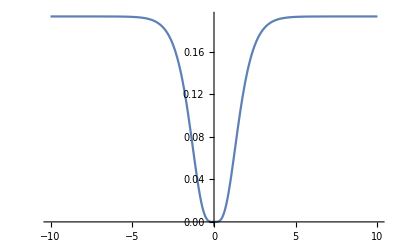

```mathematica
g[x_] = Tanh[x];
H[x_] := -1/2 * Power[Tanh[x],2] + NIntegrate[ArcTanh[V], {V, 0, Tanh[x]}]
Plot[H[x],{x,-10,10}]
```

This looks like it is always positive! Now let’s check the derivative!

-Sech[x]^2 (x-Tanh[x])^2

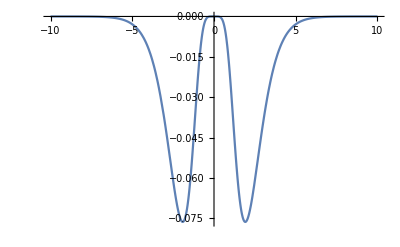

```mathematica
HD[x_] = - D[g[x],x]*Power[x-g[x],2]
Plot[HD[x],{x,-10,10}]
```

#### Part D

This is false, consider the counter-example:

```mathematica
(-1 + Tanh[1.0])Sech[1.0]^2 + Sech[1.0]^2
test[x_,y_] = x*(-x+Tanh[y])*Sech[x]^2+y*(-y+Tanh[x])*Sech[y]^2
test[0.25,5]
```

0.31985

y Sech[y]^2 (-y+Tanh[x])+x Sech[x]^2 (-x+Tanh[y])

0.171914

```mathematica
Plot3D[x*(-x+Tanh[y])*Sech[x]^2+y*(-y+Tanh[x])*Sech[y]^2,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

This go positive man, no good

## Question 6

#### Set up

Consider the Lorenz Equations

```mathematica
xt[x_,y_,z_] = 10(y - x);
yt[x_,y_,z_] = r*x - y - x*z;
zt[x_,y_,z_] = -8/3*z + x*y;
```

Find the fixed points

```mathematica
fixedPointList = Solve[xt[x,y,z]==yt[x,y,z]==zt[x,y,z]==0,{x,y,z}];
{x,y,z} /. fixedPointList
```

{{0,0,0},{-2 √(2/3) √(-1+r),-2 √(2/3) √(-1+r),-1+r},{2 √(2/3) √(-1+r),2 √(2/3) √(-1+r),-1+r}}

Define the Jacobian

```mathematica
Clear[x,y,z]
J[x_,y_,z_] = {{D[xt[x,y,z],x],D[xt[x,y,z],y],D[xt[x,y,z],z]},
{D[yt[x,y,z],x],D[yt[x,y,z],y],D[yt[x,y,z],z]},
{D[zt[x,y,z],x],D[zt[x,y,z],y],D[zt[x,y,z],z]}};

MatrixForm[J[x,y,z]]
```

(-10 | 10 | 0
r-z | -1 | -x
y | x | -8/3)

#### Fixed Point at (0,0,0)

Evaluate Jacobian at fixed point

```mathematica
evalJ = J[x,y,z] /. fixedPointList[[1]];
MatrixForm[evalJ]

partB = evalJ /. r->1;
```

(-10 | 10 | 0
r | -1 | 0
0 | 0 | -8/3)

Find eigenvalues

```mathematica
Clear[evals]
evals[r_] = Eigenvalues[evalJ]
```

{-8/3,1/2 (-11-√(81+40 r)),1/2 (-11+√(81+40 r))}

Determine Stability

{-8/3,1/2 (-11-Re[√(81+40 r)]),1/2 (-11+Re[√(81+40 r)])}<0&&r∈ℝ

r<1

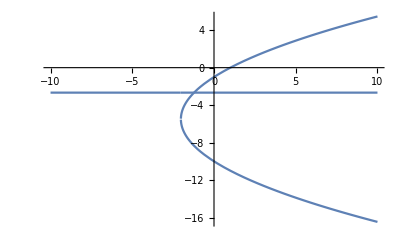

```mathematica
(*Assuming[r ∈ Reals, Reduce[Re[evals[r]]<0,r]]*)

negReEvals = Re[evals[r]] < 0 && Element[r, Reals]

Reduce[And @@ negReEvals, r]

Plot[evals[r],{r,-10,10}]
```

#### Fixed Point at (-2 √(2/3) √(-1+r),-2 √(2/3) √(-1+r),-1+r)

Evaluate Jacobian at fixed point

```mathematica
evalJ = J[x,y,z] /. fixedPointList[[2]];
MatrixForm[evalJ]
```

(-10 | 10 | 0
1 | -1 | 2 √(2/3) √(-1+r)
-2 √(2/3) √(-1+r) | -2 √(2/3) √(-1+r) | -8/3)

Find eigenvalues

```mathematica
charpoly[λ_] = CharacteristicPolynomial[evalJ,λ]
grossEvals = Solve[charpoly[λ]==0,λ];
evals1[r_] = {λ} /. grossEvals
```

160/3-(160 r)/3-(80 λ)/3-(8 r λ)/3-(41 λ^2)/3-λ^3

{{-41/9+(-961/9+8 r)/((5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3))-1/9 (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3)},{-41/9-((1+ⅈ √3) (-961/9+8 r))/(2 (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3))+1/18 (1-ⅈ √3) (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3)},{-41/9-((1-ⅈ √3) (-961/9+8 r))/(2 (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3))+1/18 (1+ⅈ √3) (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3)}}

Determine Stability

```mathematica
negReEvals = Re[evals1[r]] < 0 && Element[r, Reals];

Reduce[And @@ negReEvals, r]

(*Plot[evals[r],{r,-10,10}]*)
```

1<r<470/19

#### Fixed Point at (2 √(2/3) √(-1+r),2 √(2/3) √(-1+r),-1+r)

Evaluate Jacobian at fixed point

```mathematica
evalJ = J[x,y,z] /. fixedPointList[[3]];
MatrixForm[evalJ]
```

(-10 | 10 | 0
1 | -1 | -2 √(2/3) √(-1+r)
2 √(2/3) √(-1+r) | 2 √(2/3) √(-1+r) | -8/3)

Find eigenvalues

```mathematica
charpoly[λ_] = CharacteristicPolynomial[evalJ,λ]
grossEvals = Solve[charpoly[λ]==0,λ];
evals2[r_] = {λ} /. grossEvals
```

160/3-(160 r)/3-(80 λ)/3-(8 r λ)/3-(41 λ^2)/3-λ^3

{{-41/9+(-961/9+8 r)/((5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3))-1/9 (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3)},{-41/9-((1+ⅈ √3) (-961/9+8 r))/(2 (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3))+1/18 (1-ⅈ √3) (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3)},{-41/9-((1-ⅈ √3) (-961/9+8 r))/(2 (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3))+1/18 (1+ⅈ √3) (5201+15012 r+36 √3 √(-221310+91470 r+54119 r^2+96 r^3))^(1/3)}}

Determine Stability

```mathematica
negReEvals = Re[evals2[r]] < 0 && Element[r, Reals];

Reduce[And @@ negReEvals, r]

evals1[r] == evals2[r]

(*Plot[evals[r],{r,-10,10}]*)
```

1<r<470/19

True

### Part B

We evaluate the Jacobian at (0,0,0)

```mathematica
MatrixForm[partB]
A = partB; (*jacobian*) 
R[{x_,y_,z_}] = {0,-x*z,x*y}; (*nonlinear terms in our system*) 
sys = Eigensystem[partB]
T = Transpose[sys[[2]]]
MatrixForm[T]
```

(-10 | 10 | 0
1 | -1 | 0
0 | 0 | -8/3)

{{-11,-8/3,0},{{-10,1,0},{0,0,1},{1,1,0}}}

{{-10,0,1},{1,0,1},{0,1,0}}

(-10 | 0 | 1
1 | 0 | 1
0 | 1 | 0)

We see that the eigen pairs corresponding to -11 and -8/3 are stable while the eigen pair corresponding to 0 is a center
Now we wish to make a stable coord plane and a center coord plane

We can compute the transformation using:

```mathematica
Clear[u]
uwu = Inverse[T].A.T.{u,v,w} + Inverse[T].R[T.{u,v,w}]
MatrixForm[uwu]
```

{-11 u-1/11 v (-10 u+w),-(8 v)/3+(-10 u+w) (u+w),-10/11 v (-10 u+w)}

(-11 u-1/11 v (-10 u+w)
-(8 v)/3+(-10 u+w) (u+w)
-10/11 v (-10 u+w))

Let’s pick this a part a bit more

```mathematica
Clear[u1d,v1d,w1d]
u1d[u_,v_,w_] = uwu[[1]]
v1d[u_,v_,w_] = uwu[[2]]
w1d[u_,v_,w_] = uwu[[3]]
```

-11 u-1/11 v (-10 u+w)

-(8 v)/3+(-10 u+w) (u+w)

-10/11 v (-10 u+w)

Let’s define h and plug into 4.29 of Nard Notes

```mathematica
h[u_,v_] = a u + b v + c u v + d u^2 + ρ v^2;
grossRight = D[h[u,v],u]*u1d[u,v,w]+D[h[u,v],v]*v1d[u,v,w] /. w -> h[u,v]
grossLeft = w1d[u,v,w] /. w -> h[u,v]
(*Collect[gross,{u,v}]*)
```

(a+2 d u+c v) (-11 u-1/11 v (-10 u+a u+d u^2+b v+c u v+v^2 ρ))+(b+c u+2 v ρ) (-(8 v)/3+(-10 u+a u+d u^2+b v+c u v+v^2 ρ) (u+a u+d u^2+b v+c u v+v^2 ρ))

-10/11 v (-10 u+a u+d u^2+b v+c u v+v^2 ρ)

By looky look we see b = 0  and a = 0 because there are no linear terms in w’

```mathematica
gross1Right = grossRight /. {b -> 0, a -> 0};
gross1Left = grossLeft /. {b -> 0, a -> 0};

gross1Right
gross1Left

Solve[Coefficient[gross1Right,u*v] == Coefficient[gross1Left,u*v],c]

gross2Right = gross1Right  /. c -> -300/451
gross2Left = gross1Left /. c -> -300/451
```

(2 d u+c v) (-11 u-1/11 v (-10 u+d u^2+c u v+v^2 ρ))+(c u+2 v ρ) (-(8 v)/3+(-10 u+d u^2+c u v+v^2 ρ) (u+d u^2+c u v+v^2 ρ))

-10/11 v (-10 u+d u^2+c u v+v^2 ρ)

{{c→-300/451}}

(2 d u-(300 v)/451) (-11 u-1/11 v (-10 u+d u^2-(300 u v)/451+v^2 ρ))+(-(300 u)/451+2 v ρ) (-(8 v)/3+(-10 u+d u^2-(300 u v)/451+v^2 ρ) (u+d u^2-(300 u v)/451+v^2 ρ))

-10/11 v (-10 u+d u^2-(300 u v)/451+v^2 ρ)

```mathematica
Collect[gross2Right,u^2,Simplify]
Collect[gross2Left,u^2,Simplify]

(*u^2*d (-22) = 0*)
```

-300/451 d^2 u^5-(16 v^2 ρ)/3+(300 v^4 ρ)/4961+2 v^5 ρ^3+u^3 (3000/451+v (-810000/203401-(2 d^2)/11-18 d ρ)-(1800 v^2 (15000+203401 d ρ))/91733851)+(2 d u^4 (608850+v (90000+203401 d ρ)))/203401+(u v (45100-3000 v-16500 v^3 ρ^2+v^2 (-90000/451-902 d ρ-89298 ρ^2)))/4961+u^2 ((20 v (-203401+182655 v+18000 v^2) ρ)/203401+d (-22+(20 v)/11+(900 v^2)/4961+4 v^3 ρ^2))

-10/11 d u^2 v+(100 u v (451+30 v))/4961-(10 v^3 ρ)/11

Thus d = 0 and similarly we get ρ = 0. Therefore the finally polynomial is

```mathematica
c*u*v /. c -> -300/451
```

-(300 u v)/451